```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[22],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,13,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->-t]
```

```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[22],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[22],Table[{2n,2n},{n,3}]->t]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.0001,1,0]],B:=Inverse[β[ω,0.0001,1,0]],T1:=T1[1]},Do[J=Inverse[IdentityMatrix[22]-B.ConjugateTranspose[T1].J.T1].B,25000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[22]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[22]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[22]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[22]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

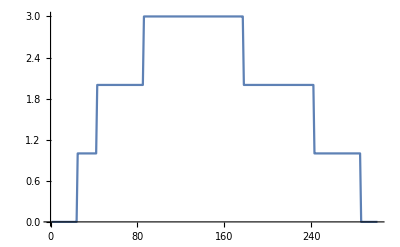

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Abs[Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]]
ListLinePlot[Table[tr[ω,0.0001,1,0],{ω,0,3,0.01}]]
```

```mathematica
Transpose[{Transpose[{{7,15},{15,16},{16,17},{17,18},{18,8}}][[2]],Transpose[{{7,15},{15,16},{16,17},{17,18},{18,8}}][[1]]}]
```

{{15,7},{16,15},{17,16},{18,17},{8,18}}

```mathematica
β81[ω_,δ_,t_,ϵ_]:=
ReplacePart[β[ω,δ,t,ϵ],Join[{{7,15},{15,16},{16,17},{17,18},{18,8}},Transpose[{Transpose[{{7,15},{15,16},{16,17},{17,18},{18,8}}][[2]],Transpose[{{7,15},{15,16},{16,17},{17,18},{18,8}}][[1]]}]]->-t]
```

```mathematica
β82[ω_,δ_,t_,ϵ_]:=
ReplacePart[β[ω,δ,t,ϵ],Join[{{14,15},{15,16},{16,17},{17,18},{18,1}},Transpose[{Transpose[{{14,15},{15,16},{16,17},{17,18},{18,1}}][[2]],Transpose[{{14,15},{15,16},{16,17},{17,18},{18,1}}][[1]]}]]->-t]
```

```mathematica
β91[ω_,δ_,t_,ϵ_]:=
ReplacePart[β[ω,δ,t,ϵ],Join[{{7,15},{15,16},{16,17},{17,18},{18,8},{1,22},{22,21},{21,20},{20,19},{19,14}},Transpose[{Transpose[{{7,15},{15,16},{16,17},{17,18},{18,8},{1,22},{22,21},{21,20},{20,19},{19,14}}][[2]],Transpose[{{7,15},{15,16},{16,17},{17,18},{18,8},{1,22},{22,21},{21,20},{20,19},{19,14}}][[1]]}]]->-t]
```

```mathematica
f[x_]:=RandomSample[Join[Flatten[Table[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14},x]],Table[imp,100-(14*x)]]]
```

```mathematica
f[3]
```

{imp,imp,imp13,imp,imp13,imp,imp10,imp1,imp12,imp7,imp,imp,imp,imp2,imp,imp,imp,imp,imp,imp,imp,imp3,imp2,imp,imp11,imp7,imp,imp14,imp,imp,imp,imp,imp6,imp,imp,imp4,imp6,imp8,imp,imp,imp,imp4,imp2,imp,imp,imp,imp8,imp,imp,imp5,imp,imp,imp,imp,imp8,imp,imp,imp,imp,imp13,imp5,imp,imp12,imp,imp,imp,imp3,imp6,imp9,imp,imp,imp,imp12,imp,imp,imp10,imp1,imp11,imp,imp4,imp3,imp7,imp11,imp14,imp,imp,imp14,imp,imp9,imp,imp10,imp1,imp9,imp,imp,imp,imp,imp5,imp,imp}

```mathematica
m[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β81[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β82[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β81[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β81[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β82[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β82[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β82[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β81[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β81[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β91[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β82[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β91[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β91[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp,imp,imp13,imp,imp13,imp,imp10,imp1,imp12,imp7,imp,imp,imp,imp2,imp,imp,imp,imp,imp,imp,imp,imp3,imp2,imp,imp11,imp7,imp,imp14,imp,imp,imp,imp,imp6,imp,imp,imp4,imp6,imp8,imp,imp,imp,imp4,imp2,imp,imp,imp,imp8,imp,imp,imp5,imp,imp,imp,imp,imp8,imp,imp,imp,imp,imp13,imp5,imp,imp12,imp,imp,imp,imp3,imp6,imp9,imp,imp,imp,imp12,imp,imp,imp10,imp1,imp11,imp,imp4,imp3,imp7,imp11,imp14,imp,imp,imp14,imp,imp9,imp,imp10,imp1,imp9,imp,imp,imp,imp,imp5,imp,imp}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[22]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[22]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[22]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
If[tra1>3,3,tra1]]
```

```mathematica
Table[{ω,m[ω,0.5]},{ω,Range[0,2,0.01]}]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,755248.-291.294 ⅈ,0.+0. ⅈ,-0.272845+384.642 ⅈ,0.+0. ⅈ,-658130.-201.857 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},«20»,{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.+0. ⅈ}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.16428×10^6-209.958 ⅈ,0.+0. ⅈ,-0.29107-12.2233 ⅈ,0.+0. ⅈ,-1.28652×10^6+253.044 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},«20»,{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.+0. ⅈ}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.18327×10^6-542.962 ⅈ,0.+0. ⅈ,-0.231395-12.9898 ⅈ,0.+0. ⅈ,-1.3123×10^6+38.0337 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},«20»,{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.+0. ⅈ}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

{{0.,1.80945×10^-7},{0.01,0.0000107425},{0.02,8.22353×10^-6},{0.03,0.00204636},{0.04,0.0419257},{0.05,0.0137019},{0.06,0.000193511},{0.07,0.00149078},{0.08,0.0370492},{0.09,1.53699×10^-7},{0.1,0.0286917},{0.11,0.0146474},{0.12,0.00423244},{0.13,0.0309258},{0.14,0.0000210171},{0.15,0.0181971},{0.16,0.0409447},{0.17,0.00463257},{0.18,0.02544},{0.19,0.00498532},{0.2,0.00322619},{0.21,0.0280964},{0.22,0.00244703},{0.23,0.232744},{0.24,0.0454738},{0.25,0.0184793},{0.26,0.0225126},{0.27,0.227151},{0.28,0.0472442},{0.29,0.0507828},{0.3,0.147454},{0.31,0.251418},{0.32,0.0511409},{0.33,0.0663133},{0.34,1.69867},{0.35,3},{0.36,0.909509},{0.37,0.479066},{0.38,1.35058},{0.39,3.13823},{0.4,3},{0.41,3},{0.42,0.599397},{0.43,3},{0.44,3},{0.45,1.40741},{0.46,2.65773},{0.47,1.20498},{0.48,0.319784},{0.49,1.52073},{0.5,1.41416},{0.51,0.0693808},{0.52,0.0458423},{0.53,0.12755},{0.54,0.990775},{0.55,0.337571},{0.56,0.147226},{0.57,0.951266},{0.58,0.722308},{0.59,0.382407},{0.6,0.142516},{0.61,0.488881},{0.62,0.0888771},{0.63,0.127246},{0.64,0.436511},{0.65,0.237837},{0.66,0.0202911},{0.67,0.674421},{0.68,0.112102},{0.69,0.708471},{0.7,0.574172},{0.71,0.643455},{0.72,0.296324},{0.73,0.590419},{0.74,1.10946},{0.75,0.232717},{0.76,0.866824},{0.77,0.0172101},{0.78,1.67317},{0.79,0.330581},{0.8,3.61663},{0.81,3},{0.82,1.76425},{0.83,3},{0.84,3},{0.85,3},{0.86,3.69287},{0.87,3.04596},{0.88,1.37281},{0.89,2.3724},{0.9,0.325763},{0.91,0.994494},{0.92,0.798454},{0.93,0.503048},{0.94,0.145201},{0.95,0.777133},{0.96,1.84295},{0.97,0.353903},{0.98,0.883379},{0.99,0.675635},{1.,1.16075},{1.01,0.73533},{1.02,0.568661},{1.03,0.890698},{1.04,0.497964},{1.05,0.619493},{1.06,0.878949},{1.07,0.745495},{1.08,0.967839},{1.09,0.0760802},{1.1,0.932189},{1.11,0.336793},{1.12,0.674369},{1.13,0.979168},{1.14,0.364883},{1.15,0.367493},{1.16,0.373454},{1.17,0.0492511},{1.18,0.145578},{1.19,0.37755},{1.2,0.110773},{1.21,0.0311619},{1.22,0.0400971},{1.23,0.121083},{1.24,0.522848},{1.25,0.0399538},{1.26,0.0775503},{1.27,0.00383182},{1.28,0.209238},{1.29,0.0251241},{1.3,0.549509},{1.31,0.762999},{1.32,0.0142157},{1.33,0.30212},{1.34,0.151433},{1.35,0.149585},{1.36,0.3166},{1.37,0.299528},{1.38,0.283176},{1.39,0.688972},{1.4,0.196811},{1.41,0.073149},{1.42,0.55185},{1.43,0.46127},{1.44,0.030378},{1.45,0.162425},{1.46,0.541069},{1.47,0.14622},{1.48,0.0841566},{1.49,0.114003},{1.5,0.627215},{1.51,0.214931},{1.52,0.516422},{1.53,0.117171},{1.54,0.346077},{1.55,0.273132},{1.56,0.0437298},{1.57,0.8492},{1.58,0.280176},{1.59,0.104299},{1.6,0.102477},{1.61,0.189171},{1.62,0.153829},{1.63,0.169002},{1.64,0.0650009},{1.65,0.408947},{1.66,0.610574},{1.67,0.0130112},{1.68,0.445272},{1.69,0.584243},{1.7,0.313364},{1.71,0.411861},{1.72,0.146539},{1.73,0.511861},{1.74,0.501277},{1.75,0.610827},{1.76,0.332483},{1.77,0.52441},{1.78,0.229789},{1.79,0.340374},{1.8,0.213211},{1.81,0.214366},{1.82,0.584215},{1.83,0.472093},{1.84,0.0858218},{1.85,0.200208},{1.86,0.143177},{1.87,0.253174},{1.88,0.241219},{1.89,0.0989959},{1.9,1.8426},{1.91,0.036538},{1.92,3.08598},{1.93,0.0418276},{1.94,1.04419},{1.95,0.049361},{1.96,0.408417},{1.97,0.362715},{1.98,0.257492},{1.99,2.64827},{2.,0.585747}}

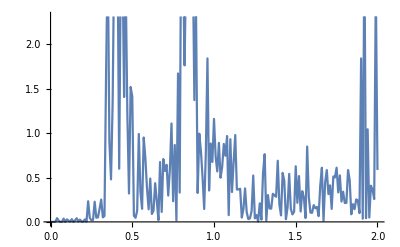

```mathematica
ListPlot[%56,Joined->True]
```

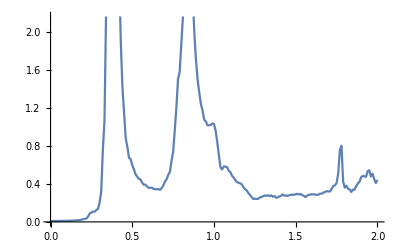

```mathematica
ListPlot[%54,Joined->True]
```

```mathematica
t
```

```mathematica
Tally[{imp,imp,imp13,imp,imp13,imp,imp10,imp1,imp12,imp7,imp,imp,imp,imp2,imp,imp,imp,imp,imp,imp,imp,imp3,imp2,imp,imp11,imp7,imp,imp14,imp,imp,imp,imp,imp6,imp,imp,imp4,imp6,imp8,imp,imp,imp,imp4,imp2,imp,imp,imp,imp8,imp,imp,imp5,imp,imp,imp,imp,imp8,imp,imp,imp,imp,imp13,imp5,imp,imp12,imp,imp,imp,imp3,imp6,imp9,imp,imp,imp,imp12,imp,imp,imp10,imp1,imp11,imp,imp4,imp3,imp7,imp11,imp14,imp,imp,imp14,imp,imp9,imp,imp10,imp1,imp9,imp,imp,imp,imp,imp5,imp,imp}]
```

{{imp,58},{imp13,3},{imp10,3},{imp1,3},{imp12,3},{imp7,3},{imp2,3},{imp3,3},{imp11,3},{imp14,3},{imp6,3},{imp4,3},{imp8,3},{imp5,3},{imp9,3}}